#### Betterplot

```mathematica
Betterplot::usage="Betterplot[{eq__},{x,min,max},{y,min,max}]";
```

```mathematica
CircleForm[eq_]:=Block[{cof=Echo[Coefficient[eq,#,2]&/@Variables[eq],"Coefficients"]},If[cof!=ConstantArray[cof[[1]],Length@cof],Print["coefficients not same"]];Echo[Transpose[{(x-h)^2+(y-k)^2==r^2,If[0==Expand[cof[[1]]((x-h)^2+(y-k)^2-r^2)-eq],"True"]}/.SolveAlways[eq/cof[[1]]==(x-h)^2+(y-k)^2-r^2,{x,y}]]]][[1]][[1]]

DiscontinuityPoints[eq_,var1_,var2_,var_:x]:=Module[{ineq=FunctionDiscontinuities[eq,var],a},a=InequalitiesToIntervals[Check[SolveValues[ineq&&var1<=var<=var2,var,Reals],Reduce[ineq&&var1<=var<=var2,var,Reals]],var];Select[{#,eq/.var->#}&/@Flatten[a[[#]]&/@Range[Length[a]]],{True,True}===Internal`RealValuedNumericQ/@#&]]

InequalitiesToIntervals[ineq_,x_]:=LogicalExpand[ineq]/. {Greater[x,foo_]->Interval[{foo,Infinity}],Greater[foo_,x]->Interval[{-Infinity,foo}],GreaterEqual[x,foo_]->Interval[{foo,Infinity}],GreaterEqual[foo_,x]->Interval[{-Infinity,foo}],Less[x,foo_]->Interval[{-Infinity,foo}],Less[foo_,x]->Interval[{foo,Infinity}],LessEqual[x,foo_]->Interval[{-Infinity,foo}],LessEqual[foo_,x]->Interval[{foo,Infinity}],Or->IntervalUnion,And->IntervalIntersection};
```

```mathematica
Options[Betterplot]=Join[Options[ContourPlot],{"Asymptote"->True,"N"->False,"TP"->True,"Time"->7,"IP"->True,"Endpoints"->True,PlotPoints->50}];

Betterplot[{eqint__},dom:{_,_?NumericQ,_?NumericQ}:{x,-10,10},ran:{_,_?NumericQ,_?NumericQ}:{y,-10,10},opts:OptionsPattern[]]:=TimeConstrained[Quiet@Module[{pairs,Tp,graphintercepts,xintercepts,hp,yintercepts,endpoints,midpoints,op,asymp,VAsymp,HAsymp,OAsymp,h,k,r,c1,C1Asymp,negx,posx,posy,negy,l,time=OptionValue["Time"],oip,ihp,IP,complex,eq},
complex=
Transpose@Table[Module[{a,eq1,trans,final},
If[Length@Variables[First[ieq]]===0,eq1=Last[ieq]==First[ieq],eq1=ieq];
Which[Exponent[First[eq1],z]===1,trans={0,0},Length[First[eq1]//First]!=2,trans={0,0},True,trans=ReIm@First@First@First[eq1]];
final={(dom[[1]]+trans[[1]])^2+(ran[[1]]+trans[[2]])^2==((Abs[Last[eq1]])^(1/Exponent[First[eq1],z]))^2,Button[Tooltip@#,Print[#]]&/@FromPolarCoordinates/@AbsArg/@SolveValues[ieq,z]}],{ieq,Select[{eqint},Variables[First[Normal@#]-Last[Normal@#]][[1]]===z&]}];

eq=Sequence[Sequence@@Select[Normal[{eqint}],Variables[First[Normal@#]-Last[Normal@#]][[1]]=!=z&]];
pairs=Subsets[{eq},{2}];
If[OptionValue["N"],
graphintercepts=Select[Normal@Table[
TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];

,
graphintercepts=Select[Normal@Table[
TimeConstrained[SolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],time,TimeConstrained[NSolveValues[Join[i,{dom[[2]]<=dom[[1]]<=dom[[3]]}],{dom[[1]],ran[[1]]},Reals],8]],
{i,pairs}],UnsameQ[#,{}]&];
xintercepts=Select[Flatten[{#,0}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.ran[[1]]->0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[1]]=!=l&];
yintercepts=Select[Flatten[{0,#}]&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->0,ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],Flatten[#][[2]]=!=l&];
negx=Select[Flatten[{dom[[2]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[2]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
posx=Select[Flatten[{dom[[3]],#}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],time,TimeConstrained[Check[NSolveValues[{i/.dom[[1]]->dom[[3]],ran[[2]]<=ran[[1]]<=ran[[3]]},ran[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[2]]=!=l&];
negy=Select[Flatten[{#,ran[[2]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[2]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
posy=Select[Flatten[{#,ran[[3]]}&/@#&/@Select[Normal@Table[
TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],time,TimeConstrained[Check[SolveValues[{i/.ran[[1]]->ran[[3]],dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]],Reals],{l}],7]],
{i,{eq}}],UnsameQ[#,{}]&],1],#[[1]]=!=l&];
];
If[OptionValue["Endpoints"],
endpoints=If[Not@ContainsAny[#,{∞,-∞}],#,##&[]]&/@DiscontinuityPoints[#,dom[[2]],dom[[3]],dom[[1]]]&/@
Flatten[SolveValues[#,ran[[1]]]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2&]],endpoints={}];

midpoints=Lookup[Association[SolveAlways[First[
QuietEcho[CircleForm[Expand[First[#]-Last[#]]]]]==(x-h)^2+(y-k)^2-r^2,{x,y}]],{h,k}]&/@Select[{eq},Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]==2&&Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]==2&];

If[OptionValue["Asymptote"],
asymp=Lookup[Merge[
OperatorApplied[ResourceFunctionHelpers`Asymptotes,{3,1,2}][dom[[1]]][ran[[1]]]
/@ReplaceAll[Rule->Equal][
Flatten[Solve[#,ran[[1]]]&/@Select[{eq},(Exponent[First[Normal@#]-Last[Normal@#],dom[[1]]]!=2)||(Exponent[First[Normal@#]-Last[Normal@#],ran[[1]]]!=2)&]]]
,Identity],{"Vertical","Horizontal","Oblique"}];

VAsymp=If[Not@MissingQ[asymp[[1]]],DeleteDuplicates[Merge[Evaluate[asymp[[1]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][dom[[1]]]],{}];
HAsymp=If[Not@MissingQ[asymp[[2]]],DeleteDuplicates[Merge[Evaluate[asymp[[2]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
OAsymp=If[Not@MissingQ[asymp[[3]]],DeleteDuplicates[Merge[Evaluate[asymp[[3]]//Flatten]/.x___±y_:>Sequence@@{(x+y),(x-y)},Identity][ran[[1]]]],{}];
C1Asymp=If[Length@Select[VAsymp,Variables[{#}]=={C[1]}&]>0,Flatten[Reap[
Table[Sow[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1==dom[[3]],C[1]]][[1]]}]],{c1,Select[VAsymp,Variables[{#}]=={C[1]}&]}]//Last]],{}];
VAsymp=Select[VAsymp,Variables[{#}]!={C[1]}&],
VAsymp={};HAsymp={};OAsymp={};C1Asymp={}];
If[OptionValue["TP"],

If[OptionValue["N"],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
Tp=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,dom[[1]]],Dt[ran[[1]],dom[[1]]]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]];
op=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
hp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,op}],1]//DeleteDuplicates;
Tp=Normal[Select[Tp,Variables[{Normal[#[[1]]]}]!={C[1]}&]],Tp={};hp={}

];
If[OptionValue["IP"],If[OptionValue["N"],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@NSolveValues[n,ran[[1]]]}/.NSolve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1],
IP=Flatten[Table[Module[{z={dom[[1]],Sequence@@SolveValues[n,ran[[1]]]}/.Solve[{SolveValues[Dt[n,{dom[[1]],2}],Dt[ran[[1]],{dom[[1]],2}]]==0,dom[[2]]<=dom[[1]]<=dom[[3]]},dom[[1]]]},If[ContainsAny[z,{dom[[1]]}]||Not@ContainsAny[Flatten[Length[#]!=2&/@z],{False}],##&[],z]],{n,{eq}}],1]
];
oip=Normal[Select[IP,Variables[{Normal[#[[1]]]}]=={C[1]}&]];
ihp=Flatten[Table[Table[Evaluate[c1/.C[1]:>x],{x,Ceiling[SolveValues[c1[[1]]==dom[[2]],C[1]]][[1]],Floor[SolveValues[c1[[1]]==dom[[3]],C[1]]][[1]]}],{c1,oip}],1]//DeleteDuplicates;
IP=Normal[Select[IP,Variables[{Normal[#[[1]]]}]!={C[1]}&]
]];
Show[{
ContourPlot[{eqint},dom,ran,Evaluate[FilterRules[{opts},Options[ContourPlot]]],PlotRange->Full,Axes->True,AxesLabel->{Row[{"ℝ | ",dom[[1]]}],Row[{"Im | ",ran[[1]]}]},PlotLegends->"Expressions",Frame->False,Ticks->Automatic,GridLines->Automatic,PlotPoints->OptionValue[PlotPoints]],

If[Not[complex==={}],Sequence@@{ContourPlot[Evaluate[complex[[1]]],dom,ran,ContourStyle->Dashed],ListPlot[complex[[2]],PlotMarkers->{Automatic,7}]},##&[]]
,

Sequence@@If[OptionValue["N"],
{
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@N@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Red},PlotMarkers->{Automatic,5}]

},
{
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@Join[Sequence@@xintercepts,Sequence@@yintercepts],PlotStyle->{Black},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates@graphintercepts,1],PlotStyle->{Blue},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@DeleteDuplicates@midpoints,PlotStyle->{Brown},PlotMarkers->{Automatic,5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Part[DeleteDuplicates[{Flatten[{posx,negx,posy,negy},1]}],1],PlotStyle->{Gray},PlotMarkers->{Automatic, 5}],
ListPlot[Button[Tooltip@#,Print[#]]&/@Flatten[DeleteDuplicates[Select[endpoints,UnsameQ[#,{}]&]],1],PlotStyle->{Green},PlotMarkers->{Automatic,5}]
}
]
,If[OptionValue["IP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Complement[Join[IP,ihp],Join[Tp,hp]],PlotStyle->{Magenta},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["TP"],ListPlot[Button[Tooltip@#,Print[#]]&/@Join[Tp,hp],PlotStyle->{Red},PlotMarkers->{Automatic,5}],##&[]],
If[OptionValue["Asymptote"]&&Length[Flatten@Join[HAsymp,OAsymp,C1Asymp,VAsymp]]!=0,
ContourPlot[
Evaluate[
Join[
If[Length[VAsymp]!=0||Length[C1Asymp]!=0,
dom[[1]]==#&/@DeleteDuplicates[Join[VAsymp,C1Asymp]],
##&[]]
,If[Length[Join[HAsymp,OAsymp]]!=0,
ran[[1]]==#&/@Join[HAsymp,OAsymp],
##&[]]
]
],
dom,ran,ContourStyle->Directive[Orange,Thick,Dashed]],##&[]]
}]],22]
SetAttributes[Betterplot,HoldFirst]
```

```mathematica
SetAttributes[Betterplot,HoldFirst]
```

#### Examples

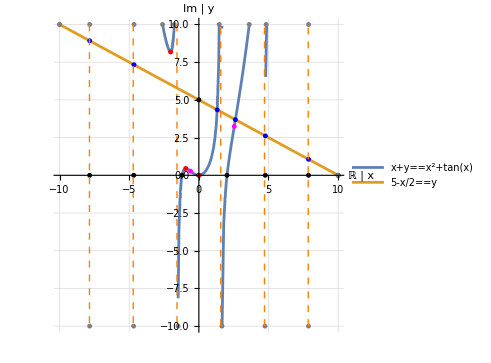

```mathematica
Betterplot[{y+x==x^2+Tan[x],5-x/2==y}]
```

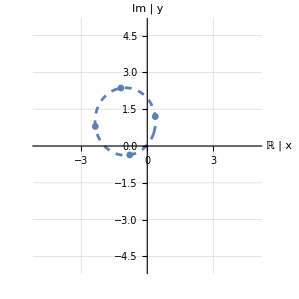

```mathematica
Betterplot[{(z-I+1)^4==3+2I},{x,-5,5},{y,-5,5}]
```